# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Spin transport\\Quantum channel\\QMB_offline.wl"]
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
LaunchKernels[14];
```

# Ising chaometer

```mathematica
J=1;
h=1.05;
L=8;
g=0.5;
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
Ha=IsingHamiltonian[1,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
neweven=Table[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=Table[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
La=1;
Lb=L-La;
sdiageigenvec=ParallelTable[sdiag[L,La,Lb,i],{i,allvecs},DistributedContexts->Full];
```

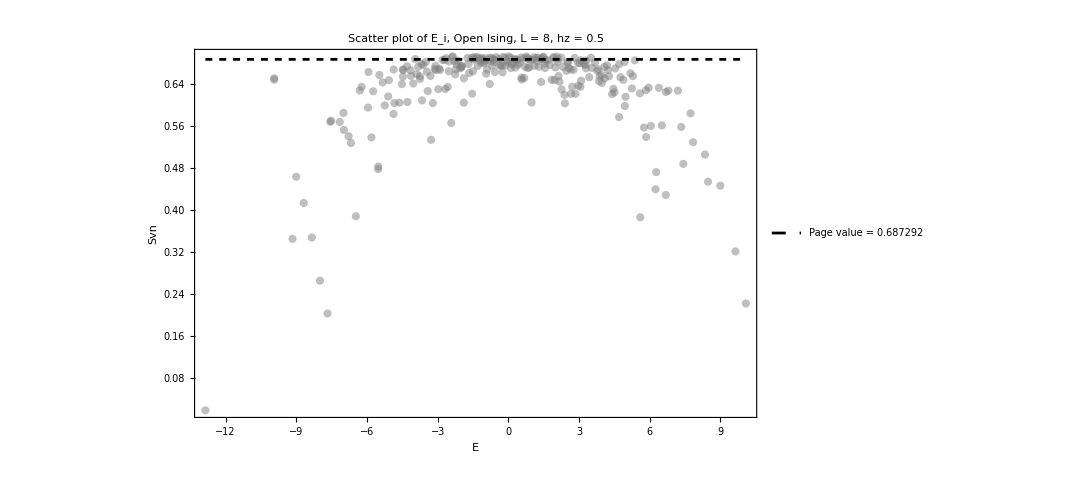

```mathematica
Show[{ListPlot[Transpose[{allvals,sdiageigenvec}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of E_i, Open Ising, L = "<>ToString[L]<>", hz = "<>ToString[g]<>"",35,Black],PlotStyle->{Directive[Gray,Opacity[0.5]]},PlotRange->All,ImageSize->800,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["Svn"]}],Plot[pageEntropy[La,Lb],{x,Min[allvals],Max[allvals]},PlotStyle->{Directive[Black,Dashed]},PlotLegends->{Style["Page value = "<>ToString[N[pageEntropy[La,Lb]]],20,Black]}]},PlotRange->All]
```

```mathematica
productstate2=Table[RandomChainProductState[L],10];
(*productstate2=Table[Flatten[KroneckerProduct[haar[1],haar[L-1]]],50];*)
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,productstate2},DistributedContexts->Full];
energies=ParallelTable[Chop[Conjugate[i].Ha.i],{i,productstate2},DistributedContexts->Full];
```

```mathematica
data=SortBy[Transpose[{iprs,energies,productstate2}],First];
productstate=data[[1;;5]][[All,3]];
```

```mathematica
tlist=Table[i,{i,0,200,0.05}];
tlist//Length
```

4001

```mathematica
fakesvn=Table[ParallelTable[{t,pur[L,La,Lb,i,allvals,allvecs,t]},{t,tlist},DistributedContexts->Full],{i,productstate}];
```

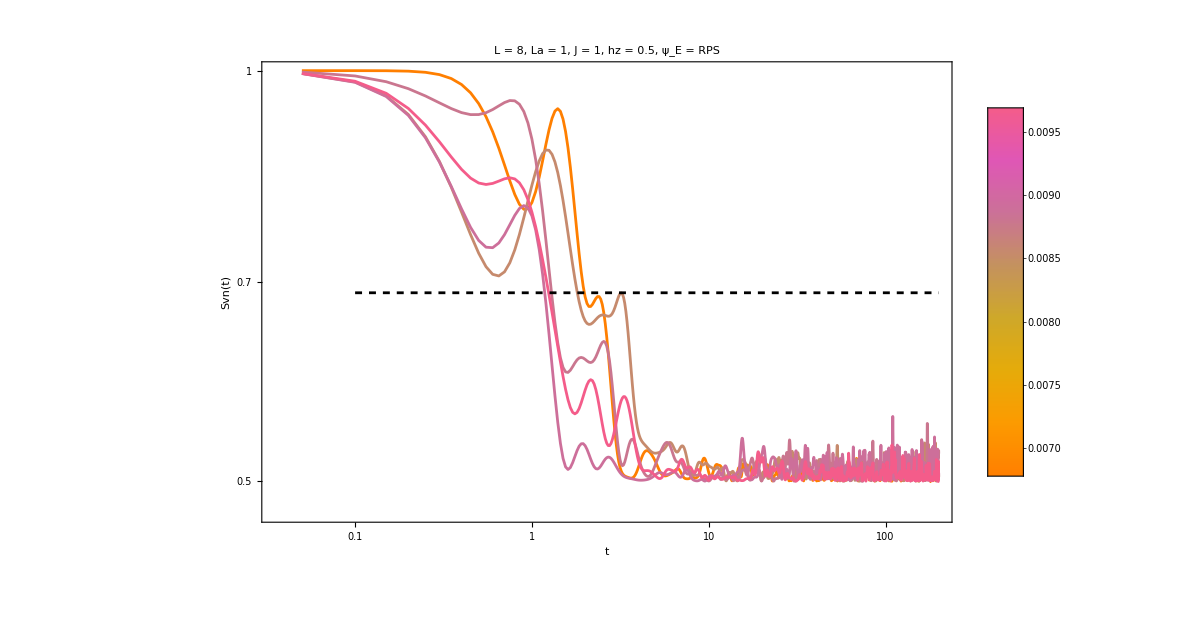

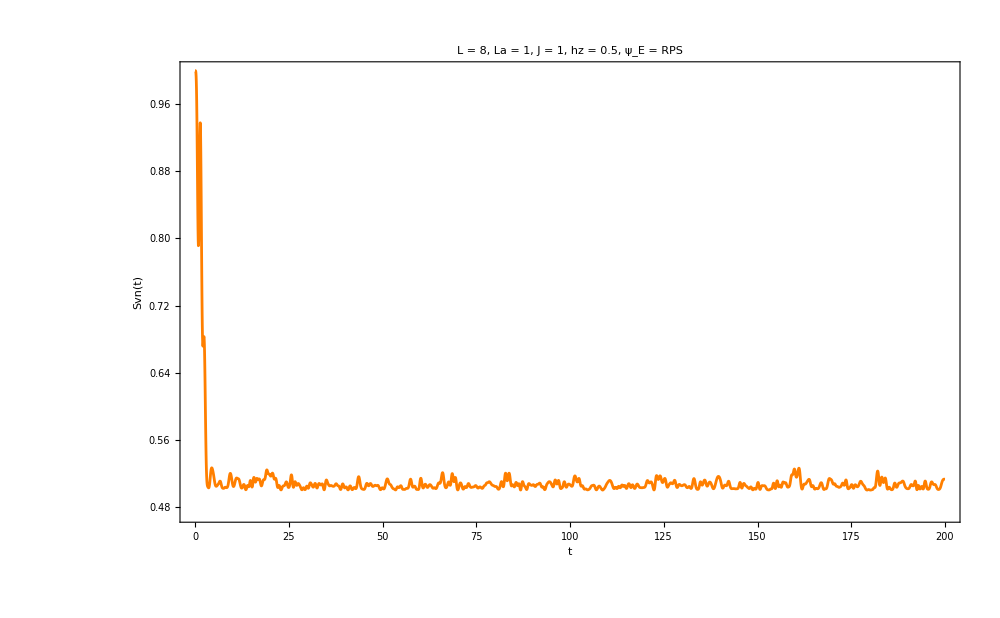

```mathematica
(*Step 1:Determine the overall energy range*)
sorted=data[[1;;5]][[All,1]];
{Emin,Emax}={Min[sorted],Max[sorted]};
(*Step 2:Define a function to map an energy value to a temperature-like color*)
colorMapping[e_]:=ColorData["FruitPunchColors"][Rescale[e,{Emin,Emax}]];
(*plot*)
plots=Table[ListLogLogPlot[fakesvn[[i]],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", ψ_E = RPS",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]]]],{i,Length[productstate]}];
Legended[Show[{plots,LogLogPlot[pageEntropy[La,Lb],{x,10^-1,Max[tlist]},PlotStyle->{Directive[Black,Dashed]}]}],BarLegend[{"FruitPunchColors",{Emin,Emax}},LabelStyle->{FontSize->12}]]
i=1;
ListPlot[fakesvn[[i]],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", ψ_E = RPS",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]]]]
```

# Choi matrix ising

## Test old

```mathematica
i=1;
ψ=productstate[[i]];
rho=Chop[MatrixPartialTrace[Dyad[ψ],1,{2^La,2^Lb}]];
```

```mathematica
{L,La,Lb}
ψ//Dimensions
rho//Dimensions
```

{5,1,4}

{32}

{16,16}

```mathematica
A=KroneckerProduct[IdentityMatrix[2^(Lb)]/2^(La),rho];
P=Transpose[allvecs];
Pinv=Conjugate[allvecs];
```

```mathematica
A//Dimensions
allvecs//Dimensions
```

{256,256}

{32,32}

```mathematica
ClearAll[U];
U[t_]:=P.DiagonalMatrix[Exp[-I*allvals*t]].Pinv;
```

```mathematica
AbsoluteTiming[chois=ParallelTable[ChoiMatrix[U[t],A,La,Lb],{t,tlist}];
truepurity=Chop[Map[Tr,Map[#.#&,chois]]];]
```

{12.0477,Null}

```mathematica
chois[[1]]//Dimensions
```

{4,4}

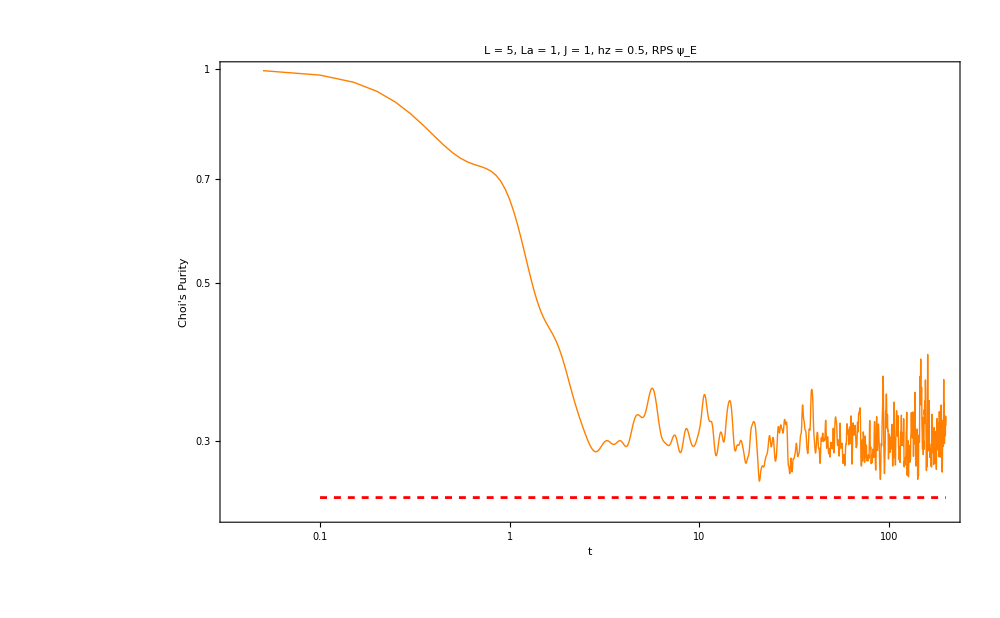

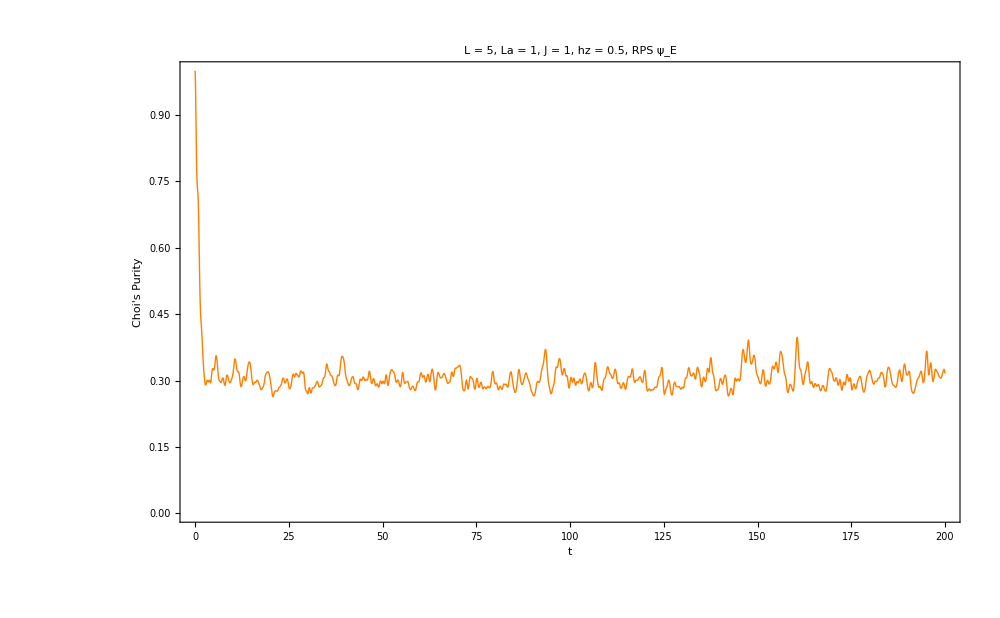

0.307297

```mathematica
plot=ListLogLogPlot[Transpose[{tlist,truepurity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", RPS ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]],Thick]];
final=Show[{plot,LogLogPlot[1/((2^La)^2),{x,10^-1,tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]}]
ListPlot[Transpose[{tlist,truepurity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", RPS ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]],Thick]]
decoherence[truepurity,tlist]
```

## Improved code c

```mathematica
Needs["Developer`"];
ClearAll[PackC];
PackC[x_]:=Developer`ToPackedArray[x];
(*1) Environment state from a global pure state|ψ⟩ on S⊗E*)
ClearAll[EnvStateFromPsi];
EnvStateFromPsi[psi_,m_Integer?Positive,n_Integer?Positive]:=PackC@Chop@MatrixPartialTrace[Dyad[psi],1,{m,n}];
(*2) Fast spectral unitary builder:U(t)=V.diag(e^{-i λ t}).V^†,implemented via column scaling (no DiagonalMatrix allocation)*)
ClearAll[SpectralUnitary];
SpectralUnitary[allvecs_,allvals_]:=Module[{P=PackC@Transpose[allvecs],Pinv=PackC@Conjugate[allvecs]},Function[{t},With[{ph=PackC@Exp[-I allvals t]},PackC@(Transpose[Transpose[P]*ph].Pinv)]]];
ClearAll[PhiProjector];
PhiProjector[m_Integer?Positive]:=Module[{phi=PackC@(Flatten[IdentityMatrix[m]]/Sqrt[m])},PackC@Dyad[phi]];
ClearAll[ChoiSysBuilder];
Options[ChoiSysBuilder]={"rhoE"->None,"psi"->None};
ChoiSysBuilder[m_Integer?Positive,n_Integer?Positive,unitaryF_Function,opts:OptionsPattern[]]:=Module[{rhoE=OptionValue["rhoE"],psi=OptionValue["psi"],projPhi,idm},If[rhoE===None&&psi===None,Message[ChoiSysBuilder::envspec];Return[$Failed]];
If[rhoE=!=None&&psi=!=None,Message[ChoiSysBuilder::envboth];Return[$Failed]];
rhoE=If[rhoE===None,EnvStateFromPsi[psi,m,n],rhoE]//PackC;
projPhi=PhiProjector[m];
idm=IdentityMatrix[m,SparseArray];(*sparse identity*)Function[{t},Module[{U=unitaryF[t],UR,Omega,X},UR=KroneckerProduct[idm,U];(*acts on R⊗S⊗E*)Omega=KroneckerProduct[projPhi,rhoE];(* |Φ⟩⟨Φ|⊗ρE*)X=UR.Omega.ConjugateTranspose[UR];
PackC@Chop@MatrixPartialTrace[X,3,{m,m,n}]]]];

ChoiSysBuilder::envspec="Provide either \"rhoE\" -> (n×n matrix) or \"psi\" -> (mn-vector).";
ChoiSysBuilder::envboth="Provide only one of \"rhoE\" or \"psi\", not both.";

ClearAll[ProcessPurity];
Options[ProcessPurity]={"Parallel"->True};
ProcessPurity[choiF_Function,tlist_List,OptionsPattern[]]:=Module[{par=TrueQ[OptionValue["Parallel"]]},If[par,ParallelMap[(Chop@Re@Tr[#.#])&@*choiF,tlist,Method->"CoarsestGrained"],Map[(Chop@Re@Tr[#.#])&@*choiF,tlist]]];
```

```mathematica
m=2^La;
n=2^Lb;
i=1;
ψ=productstate[[i]];
(*Option A:environment given as a pure global state|ψ⟩*)
rhoE=EnvStateFromPsi[ψ,m,n];
unitaryF=SpectralUnitary[allvecs,allvals];
choiF=ChoiSysBuilder[m,n,unitaryF,"rhoE"->rhoE];
```

```mathematica
(*Purity over your tlist*)
AbsoluteTiming[purity=ProcessPurity[choiF,tlist];]
```

{329.35,Null}

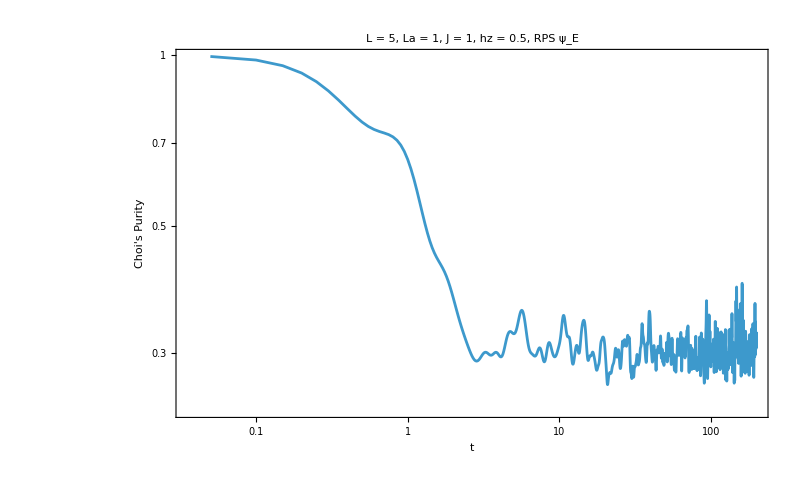

```mathematica
plot=ListLogLogPlot[Transpose[{tlist,purity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", RPS ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->800]
```

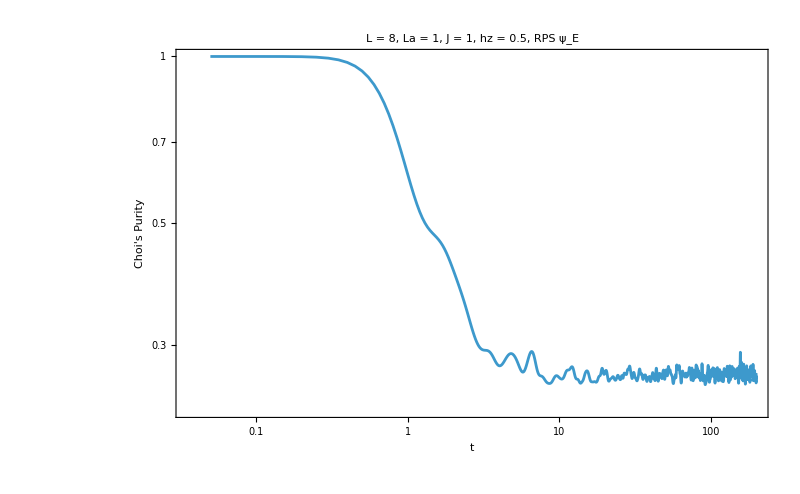

```mathematica
plot=ListLogLogPlot[Transpose[{tlist,purity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[g]<>", RPS ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->800]
```